```mathematica
Worland[r_,n_, l_]:=r^l JacobiP[n, -1/2,l-1/2,2 r^2-1]
```

```mathematica
l = 10;
n = 11;
```

```mathematica
norm[n_]:=√Integrate[Worland[z,n,l]^2/(√(1-z^2)),{z,0,1}]
```

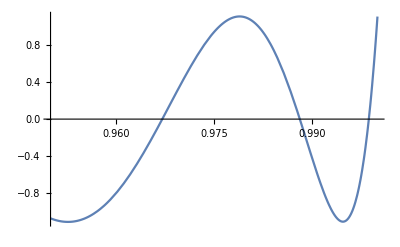

```mathematica
nn = norm[10];
Plot[Worland[r,n,l]/nn,{r,0.95,1},PlotRange->All]
```

```mathematica
nn = norm[n]^2;
A=Table[Integrate[(2 r^2-1)Worland[r, n+i, l] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={2*n*(l+n-1)/((l+2*n-2)*(l+2*n-1)),l*(l-1)/((l+2*n-1)*(l+2*n+1)),(2*n+1)*(2*l+2*n+1)/(2*(l+2*n+1)*(l+2*n+2))}
A[[2;;4]]-B
```

{0,44/93,30/341,989/2244,0}

{44/93,30/341,989/2244}

{0,0,0}

```mathematica
nn = norm[n]^2;
A=Table[Integrate[r^l Integrate[4 r/r^l Worland[r, n+i, l],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={2*(l+n-1)/((l+2*n-2)*(l+2*n-1)),-2*l/((l+2*n-1)*(l+2*n+1)),-(2*n+1)*(2*l+2*n+1)/(2*(l+n)*(l+2*n+1)*(l+2*n+2))
}
A[[2;;-2]]-B
```

{0,4/93,-20/1023,-989/47124,0}

{4/93,-20/1023,-989/47124}

{0,0,0}

```mathematica
nn = norm[n]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4 r/r^l Worland[r, n+i, l],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,3}]
B={4*(l+n-2)*(l+n-1)/((l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)),-8*l*(l+n-1)/((l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)),2*(2*l^2-4*l*n-4*n^2+1)/((l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)),2*l*(2*n+1)*(2*l+2*n+1)/((l+n)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)),(2*n+1)*(2*n+3)*(2*l+2*n+1)*(2*l+2*n+3)/(4*(l+n)*(l+n+1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4))}
A[[2;;-2]]-B
```

{0,38/18879,-160/89001,-241/173910,1978/2556477,24725/58056768,0}

{38/18879,-160/89001,-241/173910,1978/2556477,24725/58056768}

{0,0,0,0,0}

```mathematica
nn=(norm[n]^2);
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4r)/r^l Worland[r, n+i, l],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-5,5}]
B={16*(l+n-4)*(l+n-3)*(l+n-2)*(l+n-1)/((l+2*n-8)*(l+2*n-7)*(l+2*n-6)*(l+2*n-5)*(l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)),-64*l*(l+n-3)*(l+n-2)*(l+n-1)/((l+2*n-7)*(l+2*n-6)*(l+2*n-5)*(l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)),16*(l+n-2)*(l+n-1)*(6*l^2-4*l*n+4*l-4*n^2+8*n+5)/((l+2*n-6)*(l+2*n-5)*(l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)),-16*l*(l+n-1)*(4*l^2-12*l*n+6*l-12*n^2+12*n+17)/((l+2*n-5)*(l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)),2*(8*l^4-96*l^3*n-48*l^2*n^2+100*l^2+96*l*n^3-120*l*n+48*n^4-120*n^2+27)/((l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4)),4*l*(2*n+1)*(2*l+2*n+1)*(4*l^2-12*l*n-6*l-12*n^2-12*n+17)/((l+n)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4)*(l+2*n+5)),(2*n+1)*(2*n+3)*(2*l+2*n+1)*(2*l+2*n+3)*(6*l^2-4*l*n-4*l-4*n^2-8*n+5)/((l+n)*(l+n+1)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4)*(l+2*n+5)*(l+2*n+6)),l*(2*n+1)*(2*n+3)*(2*n+5)*(2*l+2*n+1)*(2*l+2*n+3)*(2*l+2*n+5)/((l+n)*(l+n+1)*(l+n+2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4)*(l+2*n+5)*(l+2*n+6)*(l+2*n+7)),(2*n+1)*(2*n+3)*(2*n+5)*(2*n+7)*(2*l+2*n+1)*(2*l+2*n+3)*(2*l+2*n+5)*(2*l+2*n+7)/(16*(l+n)*(l+n+1)*(l+n+2)*(l+n+3)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4)*(l+2*n+5)*(l+2*n+6)*(l+2*n+7)*(l+2*n+8))}
A[[2;;-2]]-B
```

{0,323/55221075,-1216/121486365,-7258/3717482769,824/95320071,1289/1694579040,-279887/82292994630,-736805/1265231145024,252625/456889024592,293045/1848009326592,0}

{323/55221075,-1216/121486365,-7258/3717482769,824/95320071,1289/1694579040,-279887/82292994630,-736805/1265231145024,252625/456889024592,293045/1848009326592}

{0,0,0,0,0,0,0,0,0}

```mathematica
lapl[f_]:=(1/r^2 D[r^2 D[f,r],r]-(l(l+1))/r^2 f)
bilapl[f_]:=lapl[lapl[f]]
```

```mathematica
nn = norm[n]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[(4 r)/r^l lapl[Worland[r, n+i, l]],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={8*(l+n-1)*(2*l+2*n-1)/((l+2*n-2)*(l+2*n-1)),8*(4*l*n+4*n^2-1)/((l+2*n-1)*(l+2*n+1)),2*(2*n+1)^2*(2*l+2*n+1)/((l+n)*(l+2*n+1)*(l+2*n+2))}
A[[2;;-2]]-B
```

{0,656/93,7384/1023,22747/11781,0}

{656/93,7384/1023,22747/11781}

{0,0,0}

```mathematica
nn=norm[n]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^l(bilapl[Worland[r, n+i, l]]//Simplify//Expand),r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,3}]
B={64*(l+n-2)*(l+n-1)*(2*l+2*n-5)*(2*l+2*n-3)/((l+2*n-4)*(l+2*n-3)*(l+2*n-2)*(l+2*n-1)),128*(l+n-1)*(2*l+2*n-3)*(4*l*n+4*n^2-4*n-3)/((l+2*n-3)*(l+2*n-2)*(l+2*n-1)*(l+2*n+1)),96*(2*n+1)*(2*l+2*n-1)*(4*l*n+2*l+4*n^2-5)/((l+2*n-2)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)),32*(2*n+1)*(2*n+3)*(2*l+2*n+1)*(4*l*n+4*l+4*n^2+4*n-3)/((l+n)*(l+2*n-1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)),4*(2*n+1)*(2*n+3)^2*(2*n+5)*(2*l+2*n+1)*(2*l+2*n+3)/((l+n)*(l+n+1)*(l+2*n+1)*(l+2*n+2)*(l+2*n+3)*(l+2*n+4))}
A[[2;;-2]]-B
```

{0,292448/6293,2918656/29667,2361272/28985,26505200/852159,1854375/403172,0}

{292448/6293,2918656/29667,2361272/28985,26505200/852159,1854375/403172}

{0,0,0,0,0}

```mathematica
laplm[laplm[r^m f[r],m],m]/r^m//Simplify//Expand
```

-(4 m f'[r])/r^3-(4 m^2 f'[r])/r^3+(4 m f''[r])/r^2+(4 m^2 f''[r])/r^2+(4 f^(3)[r])/r+(4 m f^(3)[r])/r+f^(4)[r]

```mathematica
laplm[f_]:=(1/r^2 D[r^2 D[f,r],r]-(m(m+1))/r^2 f)
```

```mathematica
laplm[f_,m_]:=(1/r^2 D[r^2 D[f,r],r]-(m(m+1))/r^2 f)
```

```mathematica
laplm[r^5 f[r],5]//Simplify//Expand
```

12 r^4 f'[r]+r^5 f''[r]

```mathematica
laplm[laplm[r^5 f[r],5],5]/r^5//Simplify//Expand
```

-(120 f'[r])/r^3+(120 f''[r])/r^2+(24 f^(3)[r])/r+f^(4)[r]

```mathematica
a1=4 √((x+1)/2)D[4 √((x+1)/2)D[4 √((x+1)/2)D[4 √((x+1)/2)D[f[x],x],x],x],x]//FullSimplify
```

16 (3 f''[x]+4 (1+x) (3 f^(3)[x]+(1+x) f^(4)[x]))

```mathematica
a2=4D[4 √((x+1)/2)D[4 √((x+1)/2)D[f[x],x],x],x]//FullSimplify
```

48 f''[x]+32 (1+x) f^(3)[x]

```mathematica
a3=4D[4D[f[x],x],x]
```

16 f''[x]

```mathematica
a1 + 4(m+1)a2+4m(m+1)a3//Expand
a1 + 4(m+1)a2+4m(m+1)a3//FullSimplify
```

240 f''[x]+256 m f''[x]+64 m^2 f''[x]+320 f^(3)[x]+128 m f^(3)[x]+320 x f^(3)[x]+128 m x f^(3)[x]+64 f^(4)[x]+128 x f^(4)[x]+64 x^2 f^(4)[x]

16 (3+2 m) (5+2 m) f''[x]+64 (1+x) ((5+2 m) f^(3)[x]+(1+x) f^(4)[x])